## Question-1:

```mathematica
SetDirectory[NotebookDirectory[]];
<<mathutils.m;
```

```mathematica
?rrDyad
```

rrDyad[{x1,y1},{x2,y2},{l1,l2},{θ1,θ2}] : Solves the RR-dyad with known points {x1,y1},{x2,y2} and link lengths l1,l2 respectively and returns the solutions for θ1,θ2 measured CCW from +ve x-axis at known points.

Module to calculate roots of a Trigonometric Polynomial : Tan Half-Angle Substitution

```mathematica
soltrigeqn2[f1_,x_]:=Module[{f2,Rlist2,t,f3,g3,g4,nn1,nn2,ii,jj,solnset},
f2=TrigExpand[f1];
Rlist2={Cos[x]-> (1-t^2)/(1+t^2),Sin[x]-> (2t)/(1+t^2)};
f3=Together[f2/.Rlist2];
g3=NSolve[Expand[Numerator[f3]]==0,t];

(* Check for the feasibility of the roots obtained *)
g4=DeleteCases[g3,_?(Im[#[[1]][[2]]]≠ 0 &)];
nn2=Length[g4];
solnset=ConstantArray[0,nn2];
For[jj=1,jj≤nn2,jj++,
solnset[[jj]]=2ArcTan[g4[[jj,1]][[2]]]];
Return[solnset];
];
```

### Functions for variable indexing (for use in loops)

```mathematica
varindex2[θ_,ii_,jj_]:=ToExpression[ToString[θ]<>ToString[ii]<>ToString[jj]];
```

```mathematica
varindex1[θ_,ii_]:=ToExpression[ToString[θ]<>ToString[ii]];
```

#### Module to solve the 3-RRR FK problem, through the concept of intersection of three circles in the plane.

```mathematica
soln3rrr[strpar_,actjvars_]:=Module[{a1,b1,a2,b2,a3,b3,a,b,θ1,θ2,θ3,xb2,yb2,xb3,yb3,lc1,xp1,yp1,α,e11,e12,e13,lc2,e21,e22,e23,lc3,e31,e32,e33,soln3rrrf,soln3rrrfc,b1xx,b1yy,b2xx,b2yy,b3xx,b3yy,phivecsol},

{a1,b1,a2,b2,a3,b3,a,b}=strpar;   
(* 'strpar' represents the list of the structural parameters for the 3-RRR manipulator with a1, a2, and a3 representing the length of the active links, starting from left and moving anti-clockwise.
b1, b2 and b3 are the length of the passive links, 'a' is the length of the side of the mobile platform equilateral triangle and 'b' is the length of the side of the base equilateral triangle *)

{θ1,θ2,θ3}=actjvars;                                    (* The list of active joint variables *)
{xb2,yb2,xb3,yb3}={b,0,b*Cos[Pi/3],b*Sin[Pi/3]};

e11=-2a1*Cos[θ1];
e12=-2a1*Sin[θ1];
e13=a1^2-b1^2;
e21=-2*xb2+2*a*Cos[α]-2*a2*Cos[θ2];
e22=-2*yb2+2*a*Sin[α]-2*a2*Sin[θ2];
e23=xb2^2+yb2^2+a^2+a2^2-b2^2-2a2*a*Cos[α]*Cos[θ2]-2a2*a*Sin[α]*Sin[θ2]-2xb2*a*Cos[α]-2yb2*a*Sin[α]+2xb2*a2*Cos[θ2]+2yb2*a2*Sin[θ2];
e31=-2*xb3+2*a*Cos[α+Pi/3]-2*a3*Cos[θ3];
e32=-2*yb3+2*a*Sin[α+Pi/3]-2*a3*Sin[θ3];
e33=xb3^2+yb3^2+a^2+a3^2-b3^2-2a3*a*Cos[α+Pi/3]*Cos[θ3]-2a3*a*Sin[α+Pi/3]*Sin[θ3]-2xb3*a*Cos[α+Pi/3]-2yb3*a*Sin[α+Pi/3]+2xb3*a3*Cos[θ3]+2yb3*a3*Sin[θ3];

(* Constraint equations *)
(* The equations of the three circles in the plane *)
(* Here our task space variables are (xp1, yp1, α), where (xp1,yp1) are the coordinates of the point 'p1' of the mobile platform and α is its orientation. *)

lc1=xp1^2+yp1^2+e11*xp1+e12*yp1+e13;
lc2=xp1^2+yp1^2+e21*xp1+e22*yp1+e23;
lc3=xp1^2+yp1^2+e31*xp1+e32*yp1+e33;

e11d=e11-e21;e12d=e12-e22;e13d=e13-e23;
e21d=e11-e31;e22d=e12-e32;e23d=e13-e33;

(* From the three circles above we get the two radical lines by the operations: (lc1-lc2) and (lc1-lc3) *)
l12=e11d*xp1+e12d*yp1+e13d;
l13=e21d*xp1+e22d*yp1+e23d;

del=e11d*e22d-e12d*e21d;
del1=e12d*e23d-e13d*e22d;
del2=e13d*e21d-e11d*e23d;

(*Finally we get to the fourth degree polynomial in Sin(α) and Cos(α)*)

pol4d=del1^2+del2^2+e11*del*del1+e12*del*del2+e13*del^2;

(* Finding the roots of the above polynomial using the module 'soltrigeqn2' *)
solnalpha=soltrigeqn2[pol4d,α];

listl12=ConstantArray[0,Length[solnalpha]];
listl13=ConstantArray[0,Length[solnalpha]];

Do[listl12[[ii]]=l12/.{α-> solnalpha[[ii]]},{ii,1,Length[solnalpha]}];
Do[listl13[[ii]]=l13/.{α-> solnalpha[[ii]]},{ii,1,Length[solnalpha]}];
solnx=ConstantArray[0,Length[solnalpha]];
solny=ConstantArray[0,Length[solnalpha]];
Do[solnx[[ii]]=Solve[{listl12[[ii]]==0,listl13[[ii]]==0},{xp1,yp1}][[1,1]][[2]],{ii,1,Length[solnalpha]}];
Do[solny[[ii]]=Solve[{listl12[[ii]]==0,listl13[[ii]]==0},{xp1,yp1}][[1,2]][[2]],{ii,1,Length[solnalpha]}];
soln3rrrf=ConstantArray[0,{Length[solnalpha],3}];
soln3rrrfc=ConstantArray[0,{Length[solnalpha],3}];
b1xx=ConstantArray[0,Length[solnalpha]];
b1yy=ConstantArray[0,Length[solnalpha]];
b2xx=ConstantArray[0,Length[solnalpha]];
b2yy=ConstantArray[0,Length[solnalpha]];
b3xx=ConstantArray[0,Length[solnalpha]];
b3yy=ConstantArray[0,Length[solnalpha]];
phivecsol=ConstantArray[0,{Length[solnalpha],3}];

(* Obtaining the values of (xp1, yp1, α) for all the solution instances *)
Do[soln3rrrf[[ii]]={solnx[[ii]],solny[[ii]],solnalpha[[ii]]},{ii,1,Length[solnalpha]}];
Do[soln3rrrfc[[ii]]={solnx[[ii]]+(a/Sqrt[3])*Cos[solnalpha[[ii]]+Pi/6],solny[[ii]]+(a/Sqrt[3])*Sin[solnalpha[[ii]]+Pi/6],solnalpha[[ii]]},{ii,1,Length[solnalpha]}];

(* Obtaining the values of (ϕ1, ϕ2, ϕ3) for all the solution instances *)
For[ii=1,ii<=Length[solnalpha],ii++,
b1xx[[ii]]=soln3rrrfc[[ii,1]]-(a/Sqrt[3])*Cos[soln3rrrfc[[ii,3]]+Pi/6];
b1yy[[ii]]=soln3rrrfc[[ii,2]]-(a/Sqrt[3])*Sin[soln3rrrfc[[ii,3]]+Pi/6];
b2xx[[ii]]=b1xx[[ii]]+a*Cos[soln3rrrfc[[ii,3]]];
b2yy[[ii]]=b1yy[[ii]]+a*Sin[soln3rrrfc[[ii,3]]];
b3xx[[ii]]=b1xx[[ii]]+a*Cos[soln3rrrfc[[ii,3]]+Pi/3];
b3yy[[ii]]=b1yy[[ii]]+a*Sin[soln3rrrfc[[ii,3]]+Pi/3];
];

For[ii=1,ii<=Length[solnalpha],ii++,
phivecsol[[ii,1]]=ArcTan[(b1xx[[ii]]-a1*Cos[θ1]),(b1yy[[ii]]-a1*Sin[θ1])];
phivecsol[[ii,2]]=ArcTan[(b2xx[[ii]]-a2*Cos[θ2]-xb2),(b2yy[[ii]]-a2*Sin[θ2]-yb2)];
phivecsol[[ii,3]]=ArcTan[(b3xx[[ii]]-a3*Cos[θ3]-xb3),(b3yy[[ii]]-a3*Sin[θ3]-yb3)];
];

For[ii=1,ii≤Length[solnalpha],ii++,
For[jj=1,jj≤3,jj++,
If[phivecsol[[ii,jj]]<0,phivecsol[[ii,jj]]=(2Pi+phivecsol[[ii,jj]]),phivecsol[[ii,jj]]=phivecsol[[ii,jj]]];
];
];
Return[phivecsol];
];
```

Demonstration of the above module through a numerical example :

l = 1/2, (Active link length)
r = 1/3, (Passive link length)
a = 1/4, (Side of the mobile platform equilateral triangle)
b = 1, (Side of the base equilateral triangle)
Theta1 = Pi/4, Theta2 = 3*Pi/4, Theta3 = 5*Pi/4.

```mathematica
strpar={1/2,1/3,1/2,1/3,1/2,1/3,1/4,1};
```

```mathematica
actjvars={Pi/4,3 Pi/4,5 Pi/4};
```

```mathematica
solnmat1=soln3rrr[strpar,actjvars]
```

{{2.04116,2.90628,0.408042},{2.2445,2.44238,1.0639},{4.40925,4.26907,5.42354},{4.50363,3.38094,4.54093},{0.242424,1.40807,0.198533},{0.434403,2.25654,5.81374}}

```mathematica
Z = {31, 21}
```

{31,21}

```mathematica
Z[[#]]&/@{1, 2}
```

{31,21}

```mathematica
{zx,zy}=(Z[[#]])&/@{1,2};
```

### (a) Mathematica module to perform the inverse kinematics of the 3-RRR planar Parallel manipulator for a given pose defined by (p;alpha).

```mathematica
threeRRRinvkin[P_?VectorQ,α_,lenvec_]:=Module[{Px,Py,xp1,yp1,xp2,yp2,xp3,yp3,l,r,a,b,xb2,yb2,xb3,yb3,e11,e12,e13,e21,e22,e23,e31,e32,e33,lc1,lc2,lc3,θ1,θ2,θ3,θ11,θ12,θ21,θ22,θ31,θ32,ϕ1,ϕ2,ϕ3,ϕ11,ϕ12,ϕ21,ϕ22,ϕ31,ϕ32,solnmat,b1x,b1y,b2x,b2y,b3x,b3y,beta1,beta2,beta3,solnmata,solnmatp},

{Px,Py}=(P[[#]])&/@{1,2};

xp1=Px-(a/Sqrt[3])*Cos[α+Pi/6];
yp1=Py-(a/Sqrt[3])*Sin[α+Pi/6];
xp2=xp1+a*Cos[α];
yp2=yp1+a*Sin[α];
xp3=xp1+a*Cos[α+Pi/3];
yp3=yp1+a*Sin[α+Pi/3];


{l,r,a,b}=(lenvec[[#]])&/@{1,2,3,4};

{xb2,yb2,xb3,yb3}={b,0,b*Cos[Pi/3],b*Sin[Pi/3]};

e11=-2l*Cos[θ1];
e12=-2l*Sin[θ1];
e13=l^2-r^2;
e21=-2*xb2+2*a*Cos[α]-2*l*Cos[θ2];
e22=-2*yb2+2*a*Sin[α]-2*l*Sin[θ2];
e23=xb2^2+yb2^2+a^2+l^2-r^2-2l*a*Cos[α]*Cos[θ2]-2l*a*Sin[α]*Sin[θ2]-2xb2*a*Cos[α]-2yb2*a*Sin[α]+2xb2*l*Cos[θ2]+2yb2*l*Sin[θ2];
e31=-2*xb3+2*a*Cos[α+Pi/3]-2*l*Cos[θ3];
e32=-2*yb3+2*a*Sin[α+Pi/3]-2*l*Sin[θ3];
e33=xb3^2+yb3^2+a^2+l^2-r^2-2l*a*Cos[α+Pi/3]*Cos[θ3]-2l*a*Sin[α+Pi/3]*Sin[θ3]-2xb3*a*Cos[α+Pi/3]-2yb3*a*Sin[α+Pi/3]+2xb3*l*Cos[θ3]+2yb3*l*Sin[θ3];

(* Constraint equations *)
(* The equations of the three circles in the plane *)
(* Here our task space variables are (xp1, yp1, α), where (xp1,yp1) are the coordinates of the point 'p1' of the mobile platform and α is its orientation. *)

lc1=xp1^2+yp1^2+e11*xp1+e12*yp1+e13;
lc2=xp1^2+yp1^2+e21*xp1+e22*yp1+e23;
lc3=xp1^2+yp1^2+e31*xp1+e32*yp1+e33;
b1x=xp1;
b1y=yp1;
b2x=xp2-xb2;
b2y=yp2-yb2;
b3x=xp3-xb3;
b3y=yp3-yb3;

(* Two values of θ1 *)
beta1=ArcTan[b1x,b1y];
θ11=beta1+ArcCos[(b1x^2+b1y^2+l^2-r^2)/(Sqrt[(2*b1x*l)^2+(2*b1y*l)^2])];
θ12=beta1-ArcCos[(b1x^2+b1y^2+l^2-r^2)/(Sqrt[(2*b1x*l)^2+(2*b1y*l)^2])];

(* Two values of ϕ1 *)
ϕ11=ArcTan[(b1x-l*Cos[θ11]),(b1y-l*Sin[θ11])];
ϕ12=ArcTan[(b1x-l*Cos[θ12]),(b1y-l*Sin[θ12])];

(* Two values of θ2 *)
beta2=ArcTan[b2x,b2y];
θ21=beta2+ArcCos[(b2x^2+b2y^2+l^2-r^2)/(Sqrt[(2*b2x*l)^2+(2*b2y*l)^2])];
θ22=beta2-ArcCos[(b2x^2+b2y^2+l^2-r^2)/(Sqrt[(2*b2x*l)^2+(2*b2y*l)^2])];

(* Two values of ϕ2 *)
ϕ21=ArcTan[(b2x-l*Cos[θ21]),(b2y-l*Sin[θ21])];
ϕ22=ArcTan[(b2x-l*Cos[θ22]),(b2y-l*Sin[θ22])];
 
(* Two values of θ3 *)
beta3=ArcTan[b3x,b3y];
θ31=beta3+ArcCos[(b3x^2+b3y^2+l^2-r^2)/(Sqrt[(2*b3x*l)^2+(2*b3y*l)^2])];
θ32=beta3-ArcCos[(b3x^2+b3y^2+l^2-r^2)/(Sqrt[(2*b3x*l)^2+(2*b3y*l)^2])];

(* Two values of ϕ3 *)
ϕ31=ArcTan[(b3x-l*Cos[θ31]),(b3y-l*Sin[θ31])];
ϕ32=ArcTan[(b3x-l*Cos[θ32]),(b3y-l*Sin[θ32])];

If[θ11<0,θ11=(2Pi+θ11),θ11=θ11];
If[θ12<0,θ12=(2Pi+θ12),θ12=θ12];
If[θ21<0,θ21=(2Pi+θ21),θ21=θ21];
If[θ22<0,θ22=(2Pi+θ22),θ22=θ22];
If[θ31<0,θ31=(2Pi+θ31),θ31=θ31];
If[θ32<0,θ32=(2Pi+θ32),θ32=θ32];

If[ϕ11<0,ϕ11=(2Pi+ϕ11),ϕ11=ϕ11];
If[ϕ12<0,ϕ12=(2Pi+ϕ12),ϕ12=ϕ12];
If[ϕ21<0,ϕ21=(2Pi+ϕ21),ϕ21=ϕ21];
If[ϕ22<0,ϕ22=(2Pi+ϕ22),ϕ22=ϕ22];
If[ϕ31<0,ϕ31=(2Pi+ϕ31),ϕ31=ϕ31];
If[ϕ32<0,ϕ32=(2Pi+ϕ32),ϕ32=ϕ32];

(* The 8 branches of Inverse kinematics solutions are returned in a matrix form with each row representing one branch *)
solnmata={{"i", "θ1", "θ2", "θ3"}, {"1", θ11, θ21, θ31}, {"2", θ11, θ21, θ32}, {"3", θ11, θ22, θ31}, {"4", θ11, θ22, θ32}, {"5", θ12, θ21, θ31}, {"6", θ12, θ21, θ32}, {"7", θ12, θ22, θ31}, {"8", θ12, θ22, θ32}};
solnmatp={{"ϕ1", "ϕ2", "ϕ3"}, {ϕ11, ϕ21, ϕ31}, {ϕ11, ϕ21, ϕ32}, {ϕ11, ϕ22, ϕ31}, {ϕ11, ϕ22, ϕ32}, {ϕ12, ϕ21, ϕ31}, {ϕ12, ϕ21, ϕ32}, {ϕ12, ϕ22, ϕ31}, {ϕ12, ϕ22, ϕ32}};
solnmat=Join[solnmata,solnmatp,2];
Return[solnmat];
];
```

```mathematica
threeRRRinvkinD[P_?VectorQ,α_,lenvec_]:=Module[{mat,solnmatda,solnmatdp,solnmatd},
mat=threeRRRinvkin[P,α,lenvec];
(*replist={θ11-> θ11*(180/Pi),θ12-> θ12*(180/Pi),θ21-> θ21*(180/Pi),θ22-> θ22*(180/Pi),θ31-> θ31*(180/Pi),θ32-> θ32*(180/Pi)};*)
(*mat2=mat/.replist;*)
solnmatda={{"i", "θ1", "θ2", "θ3"}, {"1", N[mat[[2,2]]*(180/Pi)], N[mat[[2,3]]*(180/Pi)], N[mat[[2,4]]*(180/Pi)]}, {"2", N[mat[[3,2]]*(180/Pi)], N[mat[[3,3]]*(180/Pi)], N[mat[[3,4]]*(180/Pi)]}, {"3", N[mat[[4,2]]*(180/Pi)], N[mat[[4,3]]*(180/Pi)], N[mat[[4,4]]*(180/Pi)]}, {"4", N[mat[[5,2]]*(180/Pi)], N[mat[[5,3]]*(180/Pi)], N[mat[[5,4]]*(180/Pi)]}, {"5", N[mat[[6,2]]*(180/Pi)], N[mat[[6,3]]*(180/Pi)], N[mat[[6,4]]*(180/Pi)]}, {"6", N[mat[[7,2]]*(180/Pi)], N[mat[[7,3]]*(180/Pi)], N[mat[[7,4]]*(180/Pi)]}, {"7", N[mat[[8,2]]*(180/Pi)], N[mat[[8,3]]*(180/Pi)], N[mat[[8,4]]*(180/Pi)]}, {"8", N[mat[[9,2]]*(180/Pi)], N[mat[[9,3]]*(180/Pi)], N[mat[[9,4]]*(180/Pi)]}};
solnmatdp={{"ϕ1", "ϕ2", "ϕ3"}, {N[mat[[2,5]]*(180/Pi)], N[mat[[2,6]]*(180/Pi)], N[mat[[2,7]]*(180/Pi)]}, {N[mat[[3,5]]*(180/Pi)], N[mat[[3,6]]*(180/Pi)], N[mat[[3,7]]*(180/Pi)]}, {N[mat[[4,5]]*(180/Pi)], N[mat[[4,6]]*(180/Pi)], N[mat[[4,7]]*(180/Pi)]}, {N[mat[[5,5]]*(180/Pi)], N[mat[[5,6]]*(180/Pi)], N[mat[[5,7]]*(180/Pi)]}, {N[mat[[6,5]]*(180/Pi)], N[mat[[6,6]]*(180/Pi)], N[mat[[6,7]]*(180/Pi)]}, {N[mat[[7,5]]*(180/Pi)], N[mat[[7,6]]*(180/Pi)], N[mat[[7,7]]*(180/Pi)]}, {N[mat[[8,5]]*(180/Pi)], N[mat[[8,6]]*(180/Pi)], N[mat[[8,7]]*(180/Pi)]}, {N[mat[[9,5]]*(180/Pi)], N[mat[[9,6]]*(180/Pi)], N[mat[[9,7]]*(180/Pi)]}};
solnmatd=Join[solnmatda,solnmatdp,2];
Return[solnmatd];
];
```

```mathematica
p={0.3738430060833513,0.1159317159633271};
alpha=0.4;
```

```mathematica
threeRRRinvkin[p,alpha,{1/2,1/3,1/4,1}]//MatrixForm
```

(i | θ1 | θ2 | θ3 | ϕ1 | ϕ2 | ϕ3
1 | 0.69302 | 3.62577 | 4.96186 | 4.41446 | 1.69227 | 3.5508
2 | 0.69302 | 3.62577 | 3.88828 | 4.41446 | 1.69227 | 5.29934
3 | 0.69302 | 2.25644 | 4.96186 | 4.41446 | 4.18994 | 3.5508
4 | 0.69302 | 2.25644 | 3.88828 | 4.41446 | 4.18994 | 5.29934
5 | 5.59562 | 3.62577 | 4.96186 | 1.87418 | 1.69227 | 3.5508
6 | 5.59562 | 3.62577 | 3.88828 | 1.87418 | 1.69227 | 5.29934
7 | 5.59562 | 2.25644 | 4.96186 | 1.87418 | 4.18994 | 3.5508
8 | 5.59562 | 2.25644 | 3.88828 | 1.87418 | 4.18994 | 5.29934)

```mathematica
solnmat=soln3rrr[strpar,{0.6930201173090557,3.6257693933305086,4.961862509353969}]
```

{{3.73631,2.5659,3.76343},{5.67149,0.587074,5.68441},{3.83043,2.17335,3.43962},{4.41446,1.69227,3.5508}}

```mathematica
threeRRRinvkinD[p,alpha,{1/2,1/3,1/4,1}]//MatrixForm
```

(i | θ1 | θ2 | θ3 | ϕ1 | ϕ2 | ϕ3
1 | 39.7071 | 207.741 | 284.294 | 252.93 | 96.9599 | 203.446
2 | 39.7071 | 207.741 | 222.782 | 252.93 | 96.9599 | 303.63
3 | 39.7071 | 129.285 | 284.294 | 252.93 | 240.066 | 203.446
4 | 39.7071 | 129.285 | 222.782 | 252.93 | 240.066 | 303.63
5 | 320.606 | 207.741 | 284.294 | 107.383 | 96.9599 | 203.446
6 | 320.606 | 207.741 | 222.782 | 107.383 | 96.9599 | 303.63
7 | 320.606 | 129.285 | 284.294 | 107.383 | 240.066 | 203.446
8 | 320.606 | 129.285 | 222.782 | 107.383 | 240.066 | 303.63)

Branch - 1 of the Inverse kinematics solutions, as the end-effector traverses the circular trajectory :

```mathematica
InvKinCarBr1[t_,rd_]:=Module[{pt,a,b,l,r,It,alphac,SolnBr4},
{l,r,a,b}={1/2,1/3,1/4,1};
alphac=Pi/6;

pt={(b/2)+rd*Cos[(0.5/rd)*t],(b/(2*Sqrt[3]))+rd*Sin[(0.5/rd)*t]};
It=threeRRRinvkin[pt,alphac,{l,r,a,b}];
SolnBr1=It[[2;;2,2;;7]];
Return[SolnBr1];
];
```

```mathematica
threeRRRinvkin[pt,alphac,{l,r,a,b}]
```

threeRRRinvkin[pt,alphac,{l,r,a,b}]

```mathematica
solnvec=(InvKinCarBr1[0,0.10])[[1]]
```

{0.937574,3.0247,5.48184,5.48203,0.762985,3.42498}

```mathematica
solnvec/.t-> 0
```

{0.937574,3.0247,5.48184,5.48203,0.762985,3.42498}

#### Joint-angles for r=0.10 m:

```mathematica
InvKinCarBr1[tvec[[1]],0.10]
```

Part::partd: Part specification tvec⟦1⟧ is longer than depth of object.

{{ArcCos[(5/36+(1/2-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧])^2+(-1/8+1/(2 √3)+0.1 Sin[5. tvec⟦1⟧])^2)/(√((1/2-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧])^2+(-1/8+1/(2 √3)+0.1 Sin[5. tvec⟦1⟧])^2))]+ArcTan[1/2-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧],-1/8+1/(2 √3)+0.1 Sin[5. tvec⟦1⟧]],ArcCos[(5/36+(-1/2-1/(8 √3)+(√3)/8+0.1 Cos[5. tvec⟦1⟧])^2+(1/(2 √3)+0.1 Sin[5. tvec⟦1⟧])^2)/(√((-1/2-1/(8 √3)+(√3)/8+0.1 Cos[5. tvec⟦1⟧])^2+(1/(2 √3)+0.1 Sin[5. tvec⟦1⟧])^2))]+ArcTan[-1/2-1/(8 √3)+(√3)/8+0.1 Cos[5. tvec⟦1⟧],1/(2 √3)+0.1 Sin[5. tvec⟦1⟧]],ArcCos[(5/36+(-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧])^2+(1/8+1/(2 √3)-(√3)/2+0.1 Sin[5. tvec⟦1⟧])^2)/(√((-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧])^2+(1/8+1/(2 √3)-(√3)/2+0.1 Sin[5. tvec⟦1⟧])^2))]+ArcTan[-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧],1/8+1/(2 √3)-(√3)/2+0.1 Sin[5. tvec⟦1⟧]],ArcTan[1/2-1/(8 √3)-1/2 Cos[ArcCos[(5/36+(1/2-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧])^2+(-1/8+1/(2 √3)+0.1 Sin[5. tvec⟦1⟧])^2)/(√((1/2-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧])^2+(-1/8+1/(2 √3)+0.1 Sin[5. tvec⟦1⟧])^2))]+ArcTan[1/2-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧],-1/8+1/(2 √3)+0.1 Sin[5. tvec⟦1⟧]]]+0.1 Cos[5. tvec⟦1⟧],-1/8+1/(2 √3)-1/2 Sin[ArcCos[(5/36+(1/2-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧])^2+(-1/8+1/(2 √3)+0.1 Sin[5. tvec⟦1⟧])^2)/(√((1/2-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧])^2+(-1/8+1/(2 √3)+0.1 Sin[5. tvec⟦1⟧])^2))]+ArcTan[1/2-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧],-1/8+1/(2 √3)+0.1 Sin[5. tvec⟦1⟧]]]+0.1 Sin[5. tvec⟦1⟧]],ArcTan[-1/2-1/(8 √3)+(√3)/8-1/2 Cos[ArcCos[(5/36+(-1/2-1/(8 √3)+(√3)/8+0.1 Cos[5. tvec⟦1⟧])^2+(1/(2 √3)+0.1 Sin[5. tvec⟦1⟧])^2)/(√((-1/2-1/(8 √3)+(√3)/8+0.1 Cos[5. tvec⟦1⟧])^2+(1/(2 √3)+0.1 Sin[5. tvec⟦1⟧])^2))]+ArcTan[-1/2-1/(8 √3)+(√3)/8+0.1 Cos[5. tvec⟦1⟧],1/(2 √3)+0.1 Sin[5. tvec⟦1⟧]]]+0.1 Cos[5. tvec⟦1⟧],1/(2 √3)-1/2 Sin[ArcCos[(5/36+(-1/2-1/(8 √3)+(√3)/8+0.1 Cos[5. tvec⟦1⟧])^2+(1/(2 √3)+0.1 Sin[5. tvec⟦1⟧])^2)/(√((-1/2-1/(8 √3)+(√3)/8+0.1 Cos[5. tvec⟦1⟧])^2+(1/(2 √3)+0.1 Sin[5. tvec⟦1⟧])^2))]+ArcTan[-1/2-1/(8 √3)+(√3)/8+0.1 Cos[5. tvec⟦1⟧],1/(2 √3)+0.1 Sin[5. tvec⟦1⟧]]]+0.1 Sin[5. tvec⟦1⟧]],ArcTan[-1/(8 √3)-1/2 Cos[ArcCos[(5/36+(-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧])^2+(1/8+1/(2 √3)-(√3)/2+0.1 Sin[5. tvec⟦1⟧])^2)/(√((-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧])^2+(1/8+1/(2 √3)-(√3)/2+0.1 Sin[5. tvec⟦1⟧])^2))]+ArcTan[-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧],1/8+1/(2 √3)-(√3)/2+0.1 Sin[5. tvec⟦1⟧]]]+0.1 Cos[5. tvec⟦1⟧],1/8+1/(2 √3)-(√3)/2-1/2 Sin[ArcCos[(5/36+(-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧])^2+(1/8+1/(2 √3)-(√3)/2+0.1 Sin[5. tvec⟦1⟧])^2)/(√((-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧])^2+(1/8+1/(2 √3)-(√3)/2+0.1 Sin[5. tvec⟦1⟧])^2))]+ArcTan[-1/(8 √3)+0.1 Cos[5. tvec⟦1⟧],1/8+1/(2 √3)-(√3)/2+0.1 Sin[5. tvec⟦1⟧]]]+0.1 Sin[5. tvec⟦1⟧]]}}

```mathematica
ntot=1000;
tvec={0};
theta1={InvKinCarBr1[tvec[[1]],0.10][[1,1]]};
theta2={InvKinCarBr1[tvec[[1]],0.10][[1,2]]};
theta3={InvKinCarBr1[tvec[[1]],0.10][[1,3]]};
phi1={InvKinCarBr1[tvec[[1]],0.10][[1,4]]};
phi2={InvKinCarBr1[tvec[[1]],0.10][[1,5]]};
phi3={InvKinCarBr1[tvec[[1]],0.10][[1,6]]};
For[icount=1,icount≤ntot,icount++,
tvec=Append[tvec,(3/ntot)*icount];
theta1=Append[theta1,(InvKinCarBr1[tvec[[icount+1]],0.10][[1,1]])];
theta2=Append[theta2,(InvKinCarBr1[tvec[[icount+1]],0.10][[1,2]])];
theta3=Append[theta3,(InvKinCarBr1[tvec[[icount+1]],0.10][[1,3]])];
phi1=Append[phi1,(InvKinCarBr1[tvec[[icount+1]],0.10][[1,4]])];
phi2=Append[phi2,(InvKinCarBr1[tvec[[icount+1]],0.10][[1,5]])];
phi3=Append[phi3,(InvKinCarBr1[tvec[[icount+1]],0.10][[1,6]])];
]
```

```mathematica
Dimensions[theta1]
```

{1001}

```mathematica
thetavec = Transpose[{theta1, theta2,theta3}];
thetavec//Dimensions
phivecac = Transpose[{phi1, phi2,phi3}];
phivecac//Dimensions
```

{1001,3}

{1001,3}

```mathematica
(*Since saving as a matrix is a bit pain. Flattening them out and saving them as a vector itself. Both these are originally 1001x3 matrices*)
```

```mathematica
flattheta = Flatten[thetavec];
flattheta//Dimensions
```

{3003}

```mathematica
Export["flattheta.txt",flattheta]
```

flattheta.txt

```mathematica
flatphi = Flatten[phivecac];
flatphi//Dimensions
```

{3003}

```mathematica
Export["flattheta.txt",flattheta]
```

flattheta.txt

```mathematica
Export["flatphi.csv", flatphi]
```

flatphi.csv

```mathematica
Export["thetavec.txt",thetavec];
```

```mathematica
Export["phivec.txt",phivecac];
```

```mathematica
Export["thetavec.csv",thetavec];
Export["phivec.csv",phivecac];
```

```mathematica
data1=Table[{tvec[[ii1]],theta1[[ii1]]},{ii1,1,1001}];
data2=Table[{tvec[[ii1]],theta2[[ii1]]},{ii1,1,1001}];
data3=Table[{tvec[[ii1]],theta3[[ii1]]},{ii1,1,1001}];
data4=Table[{tvec[[ii1]],phi1[[ii1]]},{ii1,1,1001}];
data5=Table[{tvec[[ii1]],phi2[[ii1]]},{ii1,1,1001}];
data6=Table[{tvec[[ii1]],phi3[[ii1]]},{ii1,1,1001}];
```

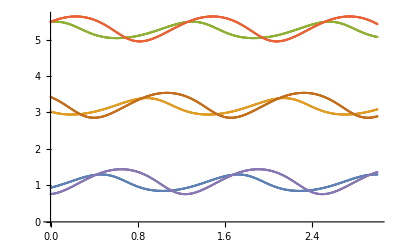

```mathematica
ListPlot[{data1,data2,data3,data4,data5,data6}]
```

```mathematica
{fn1,fn2,fn3,fn4,fn5,fn6}={Interpolation[data1],Interpolation[data2],Interpolation[data3],Interpolation[data4],Interpolation[data5],Interpolation[data6]}
```

{InterpolatingFunction[{{0., 3.}}, <>],InterpolatingFunction[{{0., 3.}}, <>],InterpolatingFunction[{{0., 3.}}, <>],InterpolatingFunction[{{0., 3.}}, <>],InterpolatingFunction[{{0., 3.}}, <>],InterpolatingFunction[{{0., 3.}}, <>]}

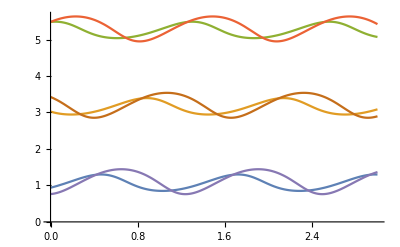

```mathematica
Plot[{fn1[t],fn2[t],fn3[t],fn4[t],fn5[t],fn6[t]},{t,0,3}]
```

```mathematica
{fn1d,fn2d,fn3d,fn4d,fn5d,fn6d}={(D[fn1[t],t]),(D[fn2[t],t]),(D[fn3[t],t]),(D[fn4[t],t]),(D[fn5[t],t]),(D[fn6[t],t])}
```

{InterpolatingFunction[{{0., 3.}}, <>][t],InterpolatingFunction[{{0., 3.}}, <>][t],InterpolatingFunction[{{0., 3.}}, <>][t],InterpolatingFunction[{{0., 3.}}, <>][t],InterpolatingFunction[{{0., 3.}}, <>][t],InterpolatingFunction[{{0., 3.}}, <>][t]}

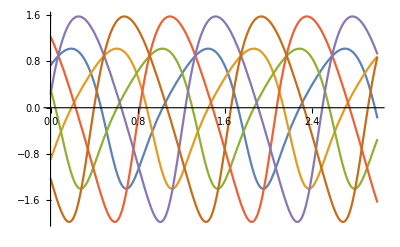

```mathematica
Plot[{fn1d,fn2d,fn3d,fn4d,fn5d,fn6d},{t,0,3}]
```

```mathematica
(* Plot showing the variation of the joint angles (θ1, θ2, θ3, Subscript[ϕ, 1], Subscript[ϕ, 2], Subscript[ϕ, 3]) w.r.t 't' in the 4th solution branch.*)

(*Plot[{theta1+2Pi,theta2,theta3+2Pi,phi1,phi2,phi3},{t,0,4Pi/5}, PlotRange-> All, PlotStyle->Thick, PlotLegends->{"θ_1(t)","θ_2(t)", "θ_3(t)", "ϕ_1(t)","ϕ_2(t)","ϕ_3(t)"},LabelStyle->Directive[Bold,Black,15], AxesLabel-> {"t ","Joint angles (rads)"}, PlotLabel->Framed[Style["Variation of the joint angles with t for Branch-4",Black,14]],ImageSize->1000]*)
```

### Formulation of equation of motion in actuator space:

## Position analysis :

Define the base point:

```mathematica
Pb1={0,0};
```

The generalized coordinates:

```mathematica
q={θ1[t],θ2[t],θ3[t],ϕ1[t],ϕ2[t],ϕ3[t]};
thetavec={θ1[t],θ2[t],θ3[t]};
phivec={ϕ1[t],ϕ2[t],ϕ3[t]};
{xb2,yb2,xb3,yb3}={b,0,b*Cos[Pi/3],b*Sin[Pi/3]};
Pb2={xb2,yb2};
Pb3={b*Cos[Pi/3],b*Sin[Pi/3]};
```

```mathematica
Pc1={(l/2)*Cos[θ1[t]],(l/2)*Sin[θ1[t]]};
Pa1={(l)*Cos[θ1[t]],(l)*Sin[θ1[t]]};
Pc2=Pa1+{(r/2)*Cos[ϕ1[t]],(r/2)*Sin[ϕ1[t]]};
Pp1=Pa1+{(r)*Cos[ϕ1[t]],(r)*Sin[ϕ1[t]]};
Ppc=Pp1+{(a/Sqrt[3])*Cos[α+Pi/6],(a/Sqrt[3])*Sin[α+Pi/6]};
Pc3=Pb2+{(l/2)*Cos[θ2[t]],(l/2)*Sin[θ2[t]]};
Pa2=Pb2+{(l)*Cos[θ2[t]],(l)*Sin[θ2[t]]};
Pc4=Pa2+{(r/2)*Cos[ϕ2[t]],(r/2)*Sin[ϕ2[t]]};
Pp2=Pa2+{(r)*Cos[ϕ2[t]],(r)*Sin[ϕ2[t]]};
Pc5=Pb3+{(l/2)*Cos[θ3[t]],(l/2)*Sin[θ3[t]]};
Pa3=Pb3+{(l)*Cos[θ3[t]],(l)*Sin[θ3[t]]};
Pc6=Pa3+{(r/2)*Cos[ϕ3[t]],(r/2)*Sin[ϕ3[t]]};
Pp3=Pa3+{(r)*Cos[ϕ3[t]],(r)*Sin[ϕ3[t]]};
```

## Velocity Analysis:

```mathematica
Jvc1=D[Pc1,{q}]
Jvc2=D[Pc3,{q}]
Jvc3=D[Pc5,{q}]
Jvc4=D[Pc2,{q}]
Jvc5=D[Pc4,{q}]
Jvc6=D[Pc6,{q}]
Jvc7=D[Ppc,{q}]
```

{{-1/2 l Sin[θ1[t]],0,0,0,0,0},{1/2 l Cos[θ1[t]],0,0,0,0,0}}

{{0,-1/2 l Sin[θ2[t]],0,0,0,0},{0,1/2 l Cos[θ2[t]],0,0,0,0}}

{{0,0,-1/2 l Sin[θ3[t]],0,0,0},{0,0,1/2 l Cos[θ3[t]],0,0,0}}

{{-l Sin[θ1[t]],0,0,-1/2 r Sin[ϕ1[t]],0,0},{l Cos[θ1[t]],0,0,1/2 r Cos[ϕ1[t]],0,0}}

{{0,-l Sin[θ2[t]],0,0,-1/2 r Sin[ϕ2[t]],0},{0,l Cos[θ2[t]],0,0,1/2 r Cos[ϕ2[t]],0}}

{{0,0,-l Sin[θ3[t]],0,0,-1/2 r Sin[ϕ3[t]]},{0,0,l Cos[θ3[t]],0,0,1/2 r Cos[ϕ3[t]]}}

{{-l Sin[θ1[t]],0,0,-r Sin[ϕ1[t]],0,0},{l Cos[θ1[t]],0,0,r Cos[ϕ1[t]],0,0}}

```mathematica
Jω1= {{0,0,0,0,0,0},{0,0,0,0,0,0},{1,0,0,0,0,0}}
Jω2= {{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,0,0,0,0}}
Jω3= {{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,1,0,0,0}}
Jω4= {{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,0,0}}
Jω5= {{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,1,0}}
Jω6= {{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1}}
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{1,0,0,0,0,0}}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,0,0,0,0}}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,1,0,0,0}}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,0,0}}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,1,0}}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1}}

## Mass/inertia matrix “M”

Defining the inertia tensors for the links:

```mathematica
Ic1 = {{0,0,0}, {0,0,0}, {0, 0, icl}};
Ic2 = {{0,0,0}, {0,0,0}, {0, 0, icl}};
Ic3 = {{0,0,0}, {0,0,0}, {0, 0, icl}};
Ic4 = {{0,0,0}, {0,0,0}, {0, 0, icr}};
Ic5 = {{0,0,0}, {0,0,0}, {0, 0, icr}};
Ic6 = {{0,0,0}, {0,0,0}, {0, 0, icr}};
```

Computing the mass matrix of the link 1:

```mathematica
M1 = Simplify[ml*Transpose[Jvc1].Jvc1] +  Simplify[Transpose[Jω1].Ic1.Jω1] ;
M1//MatrixForm
```

(icl+(l^2 ml)/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

Computing the mass matrix of the link 2:

```mathematica
M2 = Simplify[ml*Transpose[Jvc2].Jvc2] +  Simplify[Transpose[Jω2].Ic2.Jω2] ;
M2//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | icl+(l^2 ml)/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

Computing the mass matrix of the link 3:

```mathematica
M3 = Simplify[ml*Transpose[Jvc3].Jvc3] +  Simplify[Transpose[Jω3].Ic3.Jω3] ;
M3//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | icl+(l^2 ml)/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

Computing the mass matrix of the link 4:

```mathematica
M4 = Simplify[mr*Transpose[Jvc4].Jvc4] +  Simplify[Transpose[Jω4].Ic4.Jω4] ;
M4//MatrixForm
```

(l^2 mr | 0 | 0 | 1/2 l mr r Cos[θ1[t]-ϕ1[t]] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1/2 l mr r Cos[θ1[t]-ϕ1[t]] | 0 | 0 | icr+(mr r^2)/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

Computing the mass matrix of the link 5:

```mathematica
M5 = Simplify[mr*Transpose[Jvc5].Jvc5] +  Simplify[Transpose[Jω5].Ic5.Jω5] ;
M5//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | l^2 mr | 0 | 0 | 1/2 l mr r Cos[θ2[t]-ϕ2[t]] | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 l mr r Cos[θ2[t]-ϕ2[t]] | 0 | 0 | icr+(mr r^2)/4 | 0
0 | 0 | 0 | 0 | 0 | 0)

Computing the mass matrix of the link 6:

```mathematica
M6 = Simplify[mr*Transpose[Jvc6].Jvc6] +  Simplify[Transpose[Jω6].Ic6.Jω6] ;
M6//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | l^2 mr | 0 | 0 | 1/2 l mr r Cos[θ3[t]-ϕ3[t]]
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 l mr r Cos[θ3[t]-ϕ3[t]] | 0 | 0 | icr+(mr r^2)/4)

Computing the mass matrix of the link 7:

```mathematica
M7 = Simplify[mp*Transpose[Jvc7].Jvc7]  ;
M7//MatrixForm
```

(l^2 mp | 0 | 0 | l mp r Cos[θ1[t]-ϕ1[t]] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
l mp r Cos[θ1[t]-ϕ1[t]] | 0 | 0 | mp r^2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

Sum these up to create the mass matrix of the "system", i.e., the complete manipulator in this case.

```mathematica
M = Simplify[M1 + M2 + M3 +M4 +M5 +M6 +M7];
M//MatrixForm
```

(icl+1/4 l^2 (ml+4 (mp+mr)) | 0 | 0 | 1/2 l (2 mp+mr) r Cos[θ1[t]-ϕ1[t]] | 0 | 0
0 | icl+1/4 l^2 (ml+4 mr) | 0 | 0 | 1/2 l mr r Cos[θ2[t]-ϕ2[t]] | 0
0 | 0 | icl+1/4 l^2 (ml+4 mr) | 0 | 0 | 1/2 l mr r Cos[θ3[t]-ϕ3[t]]
1/2 l (2 mp+mr) r Cos[θ1[t]-ϕ1[t]] | 0 | 0 | icr+1/4 (4 mp+mr) r^2 | 0 | 0
0 | 1/2 l mr r Cos[θ2[t]-ϕ2[t]] | 0 | 0 | icr+(mr r^2)/4 | 0
0 | 0 | 1/2 l mr r Cos[θ3[t]-ϕ3[t]] | 0 | 0 | icr+(mr r^2)/4)

Check for symmetry of M

```mathematica
Simplify[M - Transpose[M]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

### Coriolis and centripetal matrix “Cmat”:

```mathematica
n = Length[q];
tempC = Table[0, {ii, 1,n}, {jj, 1,n}];
For [ii = 1, ii ≤ n, 
For[jj = 1, jj ≤ n,
For[kk = 1, kk≤ n, 
tempC[[ii,jj]] +=1/2*( D[M[[ii,jj]], q[[kk]]] + D[M[[ii,kk]], q[[jj]]] - D[M[[jj, kk]], q[[ii]]])*D[q[[kk]],t] ;
kk++];
jj++];
ii++];
```

```mathematica
Cmat =FullSimplify[tempC];
Dimensions[Cmat]
```

{6,6}

Verify the property of Cmat.

```mathematica
A = FullSimplify[D[M,t] - 2*Cmat];
Simplify[A+ Transpose[A]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

### Actuator space formulation:

```mathematica
n1=Simplify[Expand[(Pp1[[1]]-Pp2[[1]])^2+(Pp1[[2]]-Pp2[[2]])^2]]-a^2;
n2=Simplify[Expand[(Pp2[[1]]-Pp3[[1]])^2+(Pp2[[2]]-Pp3[[2]])^2]]-a^2;
n3=Simplify[Expand[(Pp3[[1]]-Pp1[[1]])^2+(Pp3[[2]]-Pp1[[2]])^2]]-a^2;
```

```mathematica
n1
```

-a^2+b^2+2 l^2+2 r^2-2 b l Cos[θ1[t]]-2 l^2 Cos[θ1[t]-θ2[t]]+2 b l Cos[θ2[t]]+2 l r Cos[θ1[t]-ϕ1[t]]-2 l r Cos[θ2[t]-ϕ1[t]]-2 b r Cos[ϕ1[t]]-2 l r Cos[θ1[t]-ϕ2[t]]+2 l r Cos[θ2[t]-ϕ2[t]]-2 r^2 Cos[ϕ1[t]-ϕ2[t]]+2 b r Cos[ϕ2[t]]

```mathematica
Jnq=D[{n1,n2,n3},{q}];
```

```mathematica
Jnq//MatrixForm
```

(2 b l Sin[θ1[t]]+2 l^2 Sin[θ1[t]-θ2[t]]-2 l r Sin[θ1[t]-ϕ1[t]]+2 l r Sin[θ1[t]-ϕ2[t]] | -2 l^2 Sin[θ1[t]-θ2[t]]-2 b l Sin[θ2[t]]+2 l r Sin[θ2[t]-ϕ1[t]]-2 l r Sin[θ2[t]-ϕ2[t]] | 0 | 2 l r Sin[θ1[t]-ϕ1[t]]-2 l r Sin[θ2[t]-ϕ1[t]]+2 b r Sin[ϕ1[t]]+2 r^2 Sin[ϕ1[t]-ϕ2[t]] | -2 l r Sin[θ1[t]-ϕ2[t]]+2 l r Sin[θ2[t]-ϕ2[t]]-2 r^2 Sin[ϕ1[t]-ϕ2[t]]-2 b r Sin[ϕ2[t]] | 0
0 | -√3 b l Cos[θ2[t]]-b l Sin[θ2[t]]+2 l^2 Sin[θ2[t]-θ3[t]]-2 l r Sin[θ2[t]-ϕ2[t]]+2 l r Sin[θ2[t]-ϕ3[t]] | √3 b l Cos[θ3[t]]-2 l^2 Sin[θ2[t]-θ3[t]]+b l Sin[θ3[t]]+2 l r Sin[θ3[t]-ϕ2[t]]-2 l r Sin[θ3[t]-ϕ3[t]] | 0 | -√3 b r Cos[ϕ2[t]]+2 l r Sin[θ2[t]-ϕ2[t]]-2 l r Sin[θ3[t]-ϕ2[t]]-b r Sin[ϕ2[t]]+2 r^2 Sin[ϕ2[t]-ϕ3[t]] | √3 b r Cos[ϕ3[t]]-2 l r Sin[θ2[t]-ϕ3[t]]+2 l r Sin[θ3[t]-ϕ3[t]]-2 r^2 Sin[ϕ2[t]-ϕ3[t]]+b r Sin[ϕ3[t]]
-√3 b l Cos[θ1[t]]+b l Sin[θ1[t]]+2 l^2 Sin[θ1[t]-θ3[t]]-2 l r Sin[θ1[t]-ϕ1[t]]+2 l r Sin[θ1[t]-ϕ3[t]] | 0 | √3 b l Cos[θ3[t]]-2 l^2 Sin[θ1[t]-θ3[t]]-b l Sin[θ3[t]]+2 l r Sin[θ3[t]-ϕ1[t]]-2 l r Sin[θ3[t]-ϕ3[t]] | -√3 b r Cos[ϕ1[t]]+2 l r Sin[θ1[t]-ϕ1[t]]-2 l r Sin[θ3[t]-ϕ1[t]]+b r Sin[ϕ1[t]]+2 r^2 Sin[ϕ1[t]-ϕ3[t]] | 0 | √3 b r Cos[ϕ3[t]]-2 l r Sin[θ1[t]-ϕ3[t]]+2 l r Sin[θ3[t]-ϕ3[t]]-2 r^2 Sin[ϕ1[t]-ϕ3[t]]-b r Sin[ϕ3[t]])

```mathematica
Jnphi=D[{n1,n2,n3},{phivec}];
```

```mathematica
Jnphi//MatrixForm
```

(2 l r Sin[θ1[t]-ϕ1[t]]-2 l r Sin[θ2[t]-ϕ1[t]]+2 b r Sin[ϕ1[t]]+2 r^2 Sin[ϕ1[t]-ϕ2[t]] | -2 l r Sin[θ1[t]-ϕ2[t]]+2 l r Sin[θ2[t]-ϕ2[t]]-2 r^2 Sin[ϕ1[t]-ϕ2[t]]-2 b r Sin[ϕ2[t]] | 0
0 | -√3 b r Cos[ϕ2[t]]+2 l r Sin[θ2[t]-ϕ2[t]]-2 l r Sin[θ3[t]-ϕ2[t]]-b r Sin[ϕ2[t]]+2 r^2 Sin[ϕ2[t]-ϕ3[t]] | √3 b r Cos[ϕ3[t]]-2 l r Sin[θ2[t]-ϕ3[t]]+2 l r Sin[θ3[t]-ϕ3[t]]-2 r^2 Sin[ϕ2[t]-ϕ3[t]]+b r Sin[ϕ3[t]]
-√3 b r Cos[ϕ1[t]]+2 l r Sin[θ1[t]-ϕ1[t]]-2 l r Sin[θ3[t]-ϕ1[t]]+b r Sin[ϕ1[t]]+2 r^2 Sin[ϕ1[t]-ϕ3[t]] | 0 | √3 b r Cos[ϕ3[t]]-2 l r Sin[θ1[t]-ϕ3[t]]+2 l r Sin[θ3[t]-ϕ3[t]]-2 r^2 Sin[ϕ1[t]-ϕ3[t]]-b r Sin[ϕ3[t]])

```mathematica
Jntheta=D[{n1,n2,n3},{thetavec}];
```

```mathematica
Jntheta//MatrixForm
```

(2 b l Sin[θ1[t]]+2 l^2 Sin[θ1[t]-θ2[t]]-2 l r Sin[θ1[t]-ϕ1[t]]+2 l r Sin[θ1[t]-ϕ2[t]] | -2 l^2 Sin[θ1[t]-θ2[t]]-2 b l Sin[θ2[t]]+2 l r Sin[θ2[t]-ϕ1[t]]-2 l r Sin[θ2[t]-ϕ2[t]] | 0
0 | -√3 b l Cos[θ2[t]]-b l Sin[θ2[t]]+2 l^2 Sin[θ2[t]-θ3[t]]-2 l r Sin[θ2[t]-ϕ2[t]]+2 l r Sin[θ2[t]-ϕ3[t]] | √3 b l Cos[θ3[t]]-2 l^2 Sin[θ2[t]-θ3[t]]+b l Sin[θ3[t]]+2 l r Sin[θ3[t]-ϕ2[t]]-2 l r Sin[θ3[t]-ϕ3[t]]
-√3 b l Cos[θ1[t]]+b l Sin[θ1[t]]+2 l^2 Sin[θ1[t]-θ3[t]]-2 l r Sin[θ1[t]-ϕ1[t]]+2 l r Sin[θ1[t]-ϕ3[t]] | 0 | √3 b l Cos[θ3[t]]-2 l^2 Sin[θ1[t]-θ3[t]]-b l Sin[θ3[t]]+2 l r Sin[θ3[t]-ϕ1[t]]-2 l r Sin[θ3[t]-ϕ3[t]])

```mathematica
Jphitheta=-Inverse[Jnphi].Jntheta;
```

```mathematica
I3=IdentityMatrix[3];
```

```mathematica
Jqtheta=Join[I3,Jphitheta];
```

```mathematica
Jqtheta//Dimensions
```

{6,3}

```mathematica
Mtheta=(Transpose[Jqtheta]).(M).(Jqtheta);
```

```mathematica
Mtheta//Dimensions
```

{3,3}

```mathematica
dJqtheta=D[Jqtheta,t];
```

```mathematica
dJqtheta//Dimensions
```

{6,3}

```mathematica
Ctheta=(Transpose[Jqtheta]).(M.dJqtheta+Cmat.Jqtheta);
```

```mathematica
Ctheta//Dimensions
```

{3,3}

```mathematica
Ta={1.25Sin[t],1.5Cos[t/2],2Cos[2t]};
```

## Numerical analysis

Set the link length data.

```mathematica
lendata = {l-> 1/2, r-> 1/3,a-> 1/4,b-> 1,tn-> 0.005};
```

Determine the inertia of links.

Consider the links to be made of solid mild-steel cylinders, of diameter "d" in metres.

```mathematica
ρ = 7800; (* density of Al: 7800 kg/m^3, approximately *)
d = 0.015; (* consider the cylinder diameter to be 20 mm *)
temp = {ml-> ρ*π*d^2/4*l, mr-> ρ*π*d^2/4*r,mp-> ρ*(Sqrt[3]/4)*a^2*tn};
massdata =Union[ {  icl-> ml*l^2/12,icr-> mr*r^2/12 }/.temp, temp]/.lendata
```

{icl→0.0143581,icr→0.00425424,ml→0.689187,mp→1.05547,mr→0.459458}

Complete data for simulation.

Combine the data sets to form a single substitution rule.

```mathematica
numdata = Union[lendata, massdata];
```

```mathematica
Jnphisubs=Det[(Jnphi/.numdata)/.{θ1[t]-> fn1[t],θ2[t]-> fn2[t],θ3[t]-> fn3[t],ϕ1[t]-> fn4[t],ϕ2[t]->fn5[t],ϕ3[t]->fn6[t]}];
```

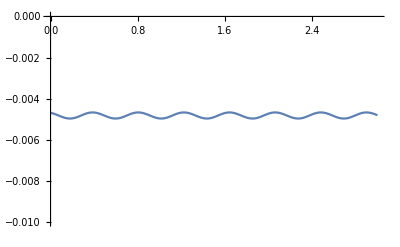

```mathematica
Plot[Jnphisubs,{t,0,3}, PlotRange->{{0,3},{-0.01,0}}]
```

```mathematica
{n1n,n2n,n3n}=({n1,n2,n3}/.{θ1[t]-> fn1[t],θ2[t]-> fn2[t],θ3[t]-> fn3[t],ϕ1[t]-> fn4[t],ϕ2[t]->fn5[t],ϕ3[t]->fn6[t]})/.numdata;
```

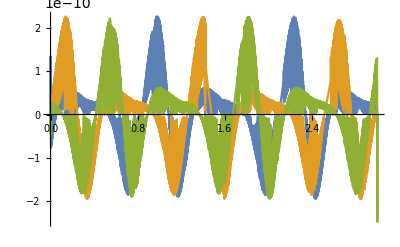

```mathematica
Plot[{n1n,n2n,n3n},{t,0,3}]
```

```mathematica
thetasubs3={θ1[t]->fn1[t],θ2[t]->fn2[t],θ3[t]->fn3[t]}
```

{θ1[t]→InterpolatingFunction[{{0., 3.}}, <>][t],θ2[t]→InterpolatingFunction[{{0., 3.}}, <>][t],θ3[t]→InterpolatingFunction[{{0., 3.}}, <>][t]}

```mathematica
thetasubs3/.t-> 0
```

{θ1[0]→0.937574,θ2[0]→3.0247,θ3[0]→5.48184}

```mathematica
fn1d/.t-> 0
```

0.728409

```mathematica
dthetasubs2={θ1'[t]->fn1d,θ2'[t]->fn2d,θ3'[t]->fn3d};
```

```mathematica
dthetasubs2/.t-> 0
```

{θ1'[0]→0.728409,θ2'[0]→-0.89674,θ3'[0]→0.316235}

```mathematica
RK4vec[fvec_,{t0_,tn_},yvec_,y0vec_,h_]:=Block[{told=t0,yoldvec=y0vec,thalf,tnew,ynewvec,k1,k2,k3,k4,sollist={{t0,y0vec}},steps},
steps=Round[(tn-t0)/h];

Do[tnew=told+h;
thalf=told+h/2;
k1=fvec/.N[{t->told,yvec[[1]]->yoldvec[[1]],yvec[[2]]->yoldvec[[2]],yvec[[3]]->yoldvec[[3]]}];
k2=fvec/.N[{t->thalf,yvec[[1]]->yoldvec[[1]]+k1[[1]]*h/2,yvec[[2]]->yoldvec[[2]]+k1[[2]]*h/2,yvec[[3]]->yoldvec[[3]]+k1[[3]]*h/2}];
k3=fvec/.N[{t->thalf,yvec[[1]]->yoldvec[[1]]+k2[[1]]*h/2,yvec[[2]]->yoldvec[[2]]+k2[[2]]*h/2,yvec[[3]]->yoldvec[[3]]+k2[[3]]*h/2}];
k4=fvec/.N[{t->tnew,yvec[[1]]->yoldvec[[1]]+k3[[1]]*h,yvec[[2]]->yoldvec[[2]]+k3[[2]]*h,yvec[[3]]->yoldvec[[3]]+k3[[3]]*h}];
ynewvec=yoldvec+(h/6)*(k1+2*k2+2*k3+k4);
sollist=Append[sollist,{tnew,ynewvec}];
told=tnew;
yoldvec=ynewvec,{steps}];

Return[sollist];
]
```

```mathematica
fvec1=((Jphitheta.(D[thetavec,t]))/.numdata)/.Union[thetasubs3,dthetasubs2];
```

```mathematica
fvec1//Dimensions
```

{3}

```mathematica
t0=0;
tn=0.001;
phivec0={fn4[t],fn5[t],fn6[t]}/.{t-> 0}
h=(tn-t0)/10
```

{5.48203,0.762985,3.42498}

0.0001

```mathematica
solvecrk4=RK4vec[fvec1,{t0,tn},phivec,phivec0, h];
```

```mathematica
solvecrk4[[-1]]
```

{0.001,{5.48325,0.763218,3.42376}}

```mathematica
thetasubs3/.t-> 0.01
```

{θ1[0.01]→0.944987,θ2[0.01]→3.016,θ3[0.01]→5.48467}

```mathematica
({n1,n2,n3}/.Union[numdata,thetasubs3,{ϕ1[t]->solvecrk4[[-1]][[2,1]] ,ϕ2[t]-> solvecrk4[[-1]][[2,2]],ϕ3[t]-> solvecrk4[[-1]][[2,3]]}])/.t-> tn
```

{4.44089×10^-16,0.,0.}

```mathematica
solIK=({fn4[t],fn5[t],fn6[t]}/.{t-> tn})
```

{5.48325,0.763218,3.42376}

```mathematica
Max[Abs[(solIK-(solvecrk4[[-1]][[2]]))]]
```

8.18932×10^-10

```mathematica
phivec
```

{ϕ1[t],ϕ2[t],ϕ3[t]}

```mathematica
phidot=D[phivec,t]-((Jphitheta.(D[thetavec,t]))/.numdata)/.Union[thetasubs3,dthetasubs2];
```

```mathematica
solnphiSysRK5 = NDSolve[{(phidot[[1]])== 0,(phidot[[2]])== 0,(phidot[[3]])==0, ϕ1[0]==phivec0[[1]], ϕ2[0]== phivec0[[2]],ϕ3[0]==phivec0[[3]]},{ϕ1,ϕ2,ϕ3},{t,0,0.001},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->6}}];
```

```mathematica
solRK5sys=({ϕ1[t],ϕ2[t],ϕ3[t]}/.solnphiSysRK5 )/.{t-> 0.001}
```

{{5.48325,0.763218,3.42376}}

```mathematica
Max[Abs[(solIK-(solRK5sys[[1]]))]]
```

8.18932×10^-10

```mathematica
thetanew={fn1[t],fn2[t],fn3[t]}/.{t-> tn}
```

{0.938304,3.0238,5.48215}

```mathematica
thetaold={fn1[t],fn2[t],fn3[t]}/.{t-> 0}
```

{0.937574,3.0247,5.48184}

```mathematica
soln3rrr[strpar,thetanew]
```

{{0.328777,1.88426,3.97082},{5.48325,0.763218,3.42376}}

```mathematica
soln3rrr[strpar,thetaold]
```

{{0.328093,1.88314,3.97228},{5.48203,0.762985,3.42498}}

```mathematica
fn1[0]
```

0.937574

#### Root-tracking through Newton-Raphson

```mathematica
nvec={n1,n2,n3}/.Union[numdata,{θ1[t]-> fn1[0.01],θ2[t]-> fn2[0.01],θ3[t]-> fn3[0.01],ϕ1[t]-> fn4[0],ϕ2[t]-> fn5[0],ϕ3[t]-> fn6[0]}]
```

{0.00207628,-0.00103371,-0.000580149}

```mathematica
RoottrackNR[thetanew_,phiold_]:=Module[{ii1,phivec,nvec,Jnphin,delphivec,phivecnew,nvecnew},
For[ii1=1,ii1≤10,ii1++,
phivec=phiold;
nvec={n1,n2,n3}/.Union[numdata,{θ1[t]-> thetanew[[1]],θ2[t]-> thetanew[[2]],θ3[t]-> thetanew[[3]],ϕ1[t]-> phivec[[1]],ϕ2[t]->  phivec[[2]],ϕ3[t]->  phivec[[3]]}];
Jnphin=Jnphi/.Union[numdata,{θ1[t]-> thetanew[[1]],θ2[t]-> thetanew[[2]],θ3[t]-> thetanew[[3]],ϕ1[t]-> phivec[[1]],ϕ2[t]->  phivec[[2]],ϕ3[t]->  phivec[[3]]}];
delphivec=LinearSolve[Jnphin,-nvec];
phivecnew=phivec+delphivec;
nvecnew={n1,n2,n3}/.Union[numdata,{θ1[t]-> thetanew[[1]],θ2[t]-> thetanew[[2]],θ3[t]-> thetanew[[3]],ϕ1[t]-> phivecnew[[1]],ϕ2[t]-> phivecnew[[2]],ϕ3[t]-> phivecnew[[3]]}];
If[Max[Abs[nvecnew]]≤10^-12,Break,phivec=phivecnew];
];
Return[phivec];
];
```

```mathematica
thetanew
```

{0.938304,3.0238,5.48215}

```mathematica
thetanew={fn1[0.01],fn2[0.01],fn3[0.01]};
phiold={fn4[0],fn5[0],fn6[0]};
```

```mathematica
RoottrackNR[thetanew,phiold]
```

{5.49398,0.765792,3.41247}

```mathematica
phivec
```

{ϕ1[t],ϕ2[t],ϕ3[t]}

#### Polynomial Continuation

```mathematica
O1 = {0,0};
L1 = {l*Cos[θ1], l*Sin[θ1]};
R1 = {r*Cos[ϕ1], r*Sin[ϕ1]};
O2 = {b,0};
L2 = {l*Cos[θ2], l*Sin[θ2]};
R2 = {r*Cos[ϕ2], r*Sin[ϕ2]};
O3 = {b*Cos[π/3], b*Sin[π/3]};
L3 = {l*Cos[θ3], l*Sin[θ3]};
R3 = {r*Cos[ϕ3], r*Sin[ϕ3]};
```

```mathematica
eq1 = (O1+L1+R1-(O2+L2+R2)).(O1+L1+R1-(O2+L2+R2))-a^2;
eq2 = (O1+L1+R1-(O3+L3+R3)).(O1+L1+R1-(O3+L3+R3))-a^2;
eq3 = (O1+O2+L2+R2-(O1+O3+L3+R3)).(O1+O2+L2+R2-(O1+O3+L3+R3))-a^2;
```

```mathematica
Variables[eq1]
Variables[eq2]
Variables[eq3]
```

{a,b,l,r,Cos[θ1],Cos[θ2],Cos[ϕ1],Cos[ϕ2],Sin[θ1],Sin[θ2],Sin[ϕ1],Sin[ϕ2]}

{a,b,l,r,Cos[θ1],Cos[θ3],Cos[ϕ1],Cos[ϕ3],Sin[θ1],Sin[θ3],Sin[ϕ1],Sin[ϕ3]}

{a,b,l,r,Cos[θ2],Cos[θ3],Cos[ϕ2],Cos[ϕ3],Sin[θ2],Sin[θ3],Sin[ϕ2],Sin[ϕ3]}

```mathematica
F= TrigExpand[Simplify[Expand[{eq1, eq2, eq3}]/.lendata]]
```

{239/144-Cos[θ1]+Cos[θ2]-1/2 Cos[θ1] Cos[θ2]-(2 Cos[ϕ1])/3+1/3 Cos[θ1] Cos[ϕ1]-1/3 Cos[θ2] Cos[ϕ1]+(2 Cos[ϕ2])/3-1/3 Cos[θ1] Cos[ϕ2]+1/3 Cos[θ2] Cos[ϕ2]-2/9 Cos[ϕ1] Cos[ϕ2]-1/2 Sin[θ1] Sin[θ2]+1/3 Sin[θ1] Sin[ϕ1]-1/3 Sin[θ2] Sin[ϕ1]-1/3 Sin[θ1] Sin[ϕ2]+1/3 Sin[θ2] Sin[ϕ2]-2/9 Sin[ϕ1] Sin[ϕ2],239/144-Cos[θ1]/2+Cos[θ3]/2-1/2 Cos[θ1] Cos[θ3]-Cos[ϕ1]/3+1/3 Cos[θ1] Cos[ϕ1]-1/3 Cos[θ3] Cos[ϕ1]+Cos[ϕ3]/3-1/3 Cos[θ1] Cos[ϕ3]+1/3 Cos[θ3] Cos[ϕ3]-2/9 Cos[ϕ1] Cos[ϕ3]-1/2 √3 Sin[θ1]+1/2 √3 Sin[θ3]-1/2 Sin[θ1] Sin[θ3]-Sin[ϕ1]/(√3)+1/3 Sin[θ1] Sin[ϕ1]-1/3 Sin[θ3] Sin[ϕ1]+Sin[ϕ3]/(√3)-1/3 Sin[θ1] Sin[ϕ3]+1/3 Sin[θ3] Sin[ϕ3]-2/9 Sin[ϕ1] Sin[ϕ3],239/144+Cos[θ2]/2-Cos[θ3]/2-1/2 Cos[θ2] Cos[θ3]+Cos[ϕ2]/3+1/3 Cos[θ2] Cos[ϕ2]-1/3 Cos[θ3] Cos[ϕ2]-Cos[ϕ3]/3-1/3 Cos[θ2] Cos[ϕ3]+1/3 Cos[θ3] Cos[ϕ3]-2/9 Cos[ϕ2] Cos[ϕ3]-1/2 √3 Sin[θ2]+1/2 √3 Sin[θ3]-1/2 Sin[θ2] Sin[θ3]-Sin[ϕ2]/(√3)+1/3 Sin[θ2] Sin[ϕ2]-1/3 Sin[θ3] Sin[ϕ2]+Sin[ϕ3]/(√3)-1/3 Sin[θ2] Sin[ϕ3]+1/3 Sin[θ3] Sin[ϕ3]-2/9 Sin[ϕ2] Sin[ϕ3]}

```mathematica
tempF= TrigExpand[Simplify[Expand[{eq1, eq2, eq3}]]]
```

{-a^2+b^2+2 l^2+2 r^2-2 b l Cos[θ1]+2 b l Cos[θ2]-2 l^2 Cos[θ1] Cos[θ2]-2 b r Cos[ϕ1]+2 l r Cos[θ1] Cos[ϕ1]-2 l r Cos[θ2] Cos[ϕ1]+2 b r Cos[ϕ2]-2 l r Cos[θ1] Cos[ϕ2]+2 l r Cos[θ2] Cos[ϕ2]-2 r^2 Cos[ϕ1] Cos[ϕ2]-2 l^2 Sin[θ1] Sin[θ2]+2 l r Sin[θ1] Sin[ϕ1]-2 l r Sin[θ2] Sin[ϕ1]-2 l r Sin[θ1] Sin[ϕ2]+2 l r Sin[θ2] Sin[ϕ2]-2 r^2 Sin[ϕ1] Sin[ϕ2],-a^2+b^2+2 l^2+2 r^2-b l Cos[θ1]+b l Cos[θ3]-2 l^2 Cos[θ1] Cos[θ3]-b r Cos[ϕ1]+2 l r Cos[θ1] Cos[ϕ1]-2 l r Cos[θ3] Cos[ϕ1]+b r Cos[ϕ3]-2 l r Cos[θ1] Cos[ϕ3]+2 l r Cos[θ3] Cos[ϕ3]-2 r^2 Cos[ϕ1] Cos[ϕ3]-√3 b l Sin[θ1]+√3 b l Sin[θ3]-2 l^2 Sin[θ1] Sin[θ3]-√3 b r Sin[ϕ1]+2 l r Sin[θ1] Sin[ϕ1]-2 l r Sin[θ3] Sin[ϕ1]+√3 b r Sin[ϕ3]-2 l r Sin[θ1] Sin[ϕ3]+2 l r Sin[θ3] Sin[ϕ3]-2 r^2 Sin[ϕ1] Sin[ϕ3],-a^2+b^2+2 l^2+2 r^2+b l Cos[θ2]-b l Cos[θ3]-2 l^2 Cos[θ2] Cos[θ3]+b r Cos[ϕ2]+2 l r Cos[θ2] Cos[ϕ2]-2 l r Cos[θ3] Cos[ϕ2]-b r Cos[ϕ3]-2 l r Cos[θ2] Cos[ϕ3]+2 l r Cos[θ3] Cos[ϕ3]-2 r^2 Cos[ϕ2] Cos[ϕ3]-√3 b l Sin[θ2]+√3 b l Sin[θ3]-2 l^2 Sin[θ2] Sin[θ3]-√3 b r Sin[ϕ2]+2 l r Sin[θ2] Sin[ϕ2]-2 l r Sin[θ3] Sin[ϕ2]+√3 b r Sin[ϕ3]-2 l r Sin[θ2] Sin[ϕ3]+2 l r Sin[θ3] Sin[ϕ3]-2 r^2 Sin[ϕ2] Sin[ϕ3]}

```mathematica
CForm[tempF]
```

List(-Power(a,2) + Power(b,2) + 2*Power(l,2) + 2*Power(r,2) - 2*b*l*Cos(θ1) + 2*b*l*Cos(θ2) - 2*Power(l,2)*Cos(θ1)*Cos(θ2) - 2*b*r*Cos(ϕ1) + 2*l*r*Cos(θ1)*Cos(ϕ1) - 2*l*r*Cos(θ2)*Cos(ϕ1) + 2*b*r*Cos(ϕ2) - 2*l*r*Cos(θ1)*Cos(ϕ2) + 
    2*l*r*Cos(θ2)*Cos(ϕ2) - 2*Power(r,2)*Cos(ϕ1)*Cos(ϕ2) - 2*Power(l,2)*Sin(θ1)*Sin(θ2) + 2*l*r*Sin(θ1)*Sin(ϕ1) - 2*l*r*Sin(θ2)*Sin(ϕ1) - 2*l*r*Sin(θ1)*Sin(ϕ2) + 2*l*r*Sin(θ2)*Sin(ϕ2) - 2*Power(r,2)*Sin(ϕ1)*Sin(ϕ2),
   -Power(a,2) + Power(b,2) + 2*Power(l,2) + 2*Power(r,2) - b*l*Cos(θ1) + b*l*Cos(θ3) - 2*Power(l,2)*Cos(θ1)*Cos(θ3) - b*r*Cos(ϕ1) + 2*l*r*Cos(θ1)*Cos(ϕ1) - 2*l*r*Cos(θ3)*Cos(ϕ1) + b*r*Cos(ϕ3) - 2*l*r*Cos(θ1)*Cos(ϕ3) + 
    2*l*r*Cos(θ3)*Cos(ϕ3) - 2*Power(r,2)*Cos(ϕ1)*Cos(ϕ3) - Sqrt(3)*b*l*Sin(θ1) + Sqrt(3)*b*l*Sin(θ3) - 2*Power(l,2)*Sin(θ1)*Sin(θ3) - Sqrt(3)*b*r*Sin(ϕ1) + 2*l*r*Sin(θ1)*Sin(ϕ1) - 2*l*r*Sin(θ3)*Sin(ϕ1) + Sqrt(3)*b*r*Sin(ϕ3) - 
    2*l*r*Sin(θ1)*Sin(ϕ3) + 2*l*r*Sin(θ3)*Sin(ϕ3) - 2*Power(r,2)*Sin(ϕ1)*Sin(ϕ3),-Power(a,2) + Power(b,2) + 2*Power(l,2) + 2*Power(r,2) + b*l*Cos(θ2) - b*l*Cos(θ3) - 2*Power(l,2)*Cos(θ2)*Cos(θ3) + b*r*Cos(ϕ2) + 2*l*r*Cos(θ2)*Cos(ϕ2) - 
    2*l*r*Cos(θ3)*Cos(ϕ2) - b*r*Cos(ϕ3) - 2*l*r*Cos(θ2)*Cos(ϕ3) + 2*l*r*Cos(θ3)*Cos(ϕ3) - 2*Power(r,2)*Cos(ϕ2)*Cos(ϕ3) - Sqrt(3)*b*l*Sin(θ2) + Sqrt(3)*b*l*Sin(θ3) - 2*Power(l,2)*Sin(θ2)*Sin(θ3) - Sqrt(3)*b*r*Sin(ϕ2) + 
    2*l*r*Sin(θ2)*Sin(ϕ2) - 2*l*r*Sin(θ3)*Sin(ϕ2) + Sqrt(3)*b*r*Sin(ϕ3) - 2*l*r*Sin(θ2)*Sin(ϕ3) + 2*l*r*Sin(θ3)*Sin(ϕ3) - 2*Power(r,2)*Sin(ϕ2)*Sin(ϕ3))

```mathematica
trigrep[i_]:={Cos[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ToExpression[Symbol[ToString[lambda]<>ToString[i]]],Sin[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ToExpression[Symbol[ToString[mu]<>ToString[i]]],Sec[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> 1/(ToExpression[Symbol[ToString[lambda]<>ToString[i]]]),Csc[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> 1/(ToExpression[Symbol[ToString[mu]<>ToString[i]]]),Tan[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ((ToExpression[Symbol[ToString[mu]<>ToString[i]]])/(ToExpression[Symbol[ToString[lambda]<>ToString[i]]])),Cot[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ((ToExpression[Symbol[ToString[lambda]<>ToString[i]]])/(ToExpression[Symbol[ToString[mu]<>ToString[i]]]))};
alpharep[i_]:={ToExpression[Symbol[ToString[α]<>ToString[i]]]-> ToExpression[Symbol[ToString[alpha]<>ToString[i]]]};
alpharepall=Union[alpharep[1],alpharep[2],alpharep[3],alpharep[4],alpharep[5],alpharep[6]];
revtrigrep[i_]:=Reverse[trigrep[i],2];
trigrepall=Union[trigrep[1],trigrep[2],trigrep[3],trigrep[4],trigrep[5],trigrep[6]];
revtrigrepall=Union[revtrigrep[1],revtrigrep[2],revtrigrep[3],revtrigrep[4],revtrigrep[5],revtrigrep[6]];
replist=Union[{Power-> pow},trigrepall,{Sin[x_]-> sin[x]},{Cos[x_]-> cos[x]},{Tan[x_]-> tan[x]},{Csc[x_]-> 1/sin[x]},{Sec[x_]-> 1/cos[x]},{Cot[x_]->sin[x]/cos[x]} ];
revreplist=Reverse[replist,2];
revalpharepall=Reverse[alpharepall,2];
inversetrig =  Union[{ArcTan[x_, y_]->atan2[y,x]} , {ArcCos[x_]->acos[x]}];
```

Symbol::symname: The string "0.41" cannot be used for a symbol name. A symbol name must start with a letter followed by letters and numbers.

ToExpression::notstrbox: Symbol[0.41] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Symbol::symname: The string "0.42" cannot be used for a symbol name. A symbol name must start with a letter followed by letters and numbers.

ToExpression::notstrbox: Symbol[0.42] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Symbol::symname: The string "0.43" cannot be used for a symbol name. A symbol name must start with a letter followed by letters and numbers.

General::stop: Further output of Symbol::symname will be suppressed during this calculation.

ToExpression::notstrbox: Symbol[0.43] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

```mathematica
angsubs = {θ1->th1, θ2->th2, θ3->th3, ϕ1->ph1, ϕ2->ph2, ϕ3->ph3}
```

{θ1→th1,θ2→th2,θ3→th3,ϕ1→ph1,ϕ2→ph2,ϕ3→ph3}

```mathematica
tempFp = CForm[tempF/.replist/.angsubs]
```

List(-2*b*r*cos(ph1) + 2*b*r*cos(ph2) - 2*b*l*cos(th1) + 2*l*r*cos(ph1)*cos(th1) - 2*l*r*cos(ph2)*cos(th1) + 2*b*l*cos(th2) - 2*l*r*cos(ph1)*cos(th2) + 2*l*r*cos(ph2)*cos(th2) - pow(a,2) + pow(b,2) + 2*pow(l,2) - 
    2*cos(th1)*cos(th2)*pow(l,2) + 2*pow(r,2) - 2*cos(ph1)*cos(ph2)*pow(r,2) - 2*pow(r,2)*sin(ph1)*sin(ph2) + 2*l*r*sin(ph1)*sin(th1) - 2*l*r*sin(ph2)*sin(th1) - 2*l*r*sin(ph1)*sin(th2) + 2*l*r*sin(ph2)*sin(th2) - 
    2*pow(l,2)*sin(th1)*sin(th2),-(b*r*cos(ph1)) + b*r*cos(ph3) - b*l*cos(th1) + 2*l*r*cos(ph1)*cos(th1) - 2*l*r*cos(ph3)*cos(th1) + b*l*cos(th3) - 2*l*r*cos(ph1)*cos(th3) + 2*l*r*cos(ph3)*cos(th3) - pow(a,2) + pow(b,2) + 2*pow(l,2) - 
    2*cos(th1)*cos(th3)*pow(l,2) + 2*pow(r,2) - 2*cos(ph1)*cos(ph3)*pow(r,2) - b*r*pow(3,0.5)*sin(ph1) + b*r*pow(3,0.5)*sin(ph3) - 2*pow(r,2)*sin(ph1)*sin(ph3) - b*l*pow(3,0.5)*sin(th1) + 2*l*r*sin(ph1)*sin(th1) - 
    2*l*r*sin(ph3)*sin(th1) + b*l*pow(3,0.5)*sin(th3) - 2*l*r*sin(ph1)*sin(th3) + 2*l*r*sin(ph3)*sin(th3) - 2*pow(l,2)*sin(th1)*sin(th3),
   b*r*cos(ph2) - b*r*cos(ph3) + b*l*cos(th2) + 2*l*r*cos(ph2)*cos(th2) - 2*l*r*cos(ph3)*cos(th2) - b*l*cos(th3) - 2*l*r*cos(ph2)*cos(th3) + 2*l*r*cos(ph3)*cos(th3) - pow(a,2) + pow(b,2) + 2*pow(l,2) - 2*cos(th2)*cos(th3)*pow(l,2) + 
    2*pow(r,2) - 2*cos(ph2)*cos(ph3)*pow(r,2) - b*r*pow(3,0.5)*sin(ph2) + b*r*pow(3,0.5)*sin(ph3) - 2*pow(r,2)*sin(ph2)*sin(ph3) - b*l*pow(3,0.5)*sin(th2) + 2*l*r*sin(ph2)*sin(th2) - 2*l*r*sin(ph3)*sin(th2) + b*l*pow(3,0.5)*sin(th3) - 
    2*l*r*sin(ph2)*sin(th3) + 2*l*r*sin(ph3)*sin(th3) - 2*pow(l,2)*sin(th2)*sin(th3))

```mathematica
Export["Fvec.txt", tempFp]
```

Fvec.txt

```mathematica
tempJ = CForm[D[F, {phi}]/.replist]/.angsubs
```

List(0,0,0)

```mathematica
Export["Jvec.txt", tempJ]
```

Jvec.txt

```mathematica
F//Dimensions
```

{3}

```mathematica
theta = {θ1, θ2, θ3};
phi = {ϕ1, ϕ2, ϕ3};
```

```mathematica
thetai = thetavec;
phii = phivecac[[1, All]];
```

```mathematica
RoottrackPC[f_, theta_, phi_, thetai_,phii_]:=Module[{loopcounter, phivals, i, thetavec, fn, Jn, phivec, fvec, nvec, Jmat, δphi, phinew},
phivals = {};
phivec = phii;
For[i=1, i≤Dimensions[thetai][[1]] ,i++,
thetavec = thetai[[i, All]];
fn = f/.Inner[Rule, theta, thetavec, List];
Jn = D[fn, {phi}];
fvec = 1;
loopcounter=0;
While[Max[Abs[fvec]]≥ 10^-12,
loopcounter++;
nvec = fn/.Inner[Rule, phi, phivec, List];
Jmat=Jn/.Inner[Rule, phi, phivec, List];
δphi=LinearSolve[Jmat,nvec];
phinew=phivec-δphi;
phivec = phinew;
fvec = fn/.Inner[Rule, phi, phivec, List];
If[loopcounter≥ 100, Break];
];
AppendTo[phivals,phivec]
];
Return[phivals];
];
```

```mathematica
phisolsnr = RoottrackPC[F, theta, phi, thetai, phii];
```

Inner::heads: Heads θ1 and List at positions 3 and 2 are expected to be the same.

ReplaceAll::reps: {Inner[Rule,{θ1,θ2,θ3},θ1[t],List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::ivar: 5.48203 is not a valid variable.

General::ivar: 0.762985 is not a valid variable.

General::ivar: 3.42498 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

LinearSolve::matrix: Argument {∂_5.48203 ({1.67618-1.00897 Cos[θ1]+1.00897 Cos[θ2]-1/2 Cos[θ1] Cos[θ2]-0.469748 Sin[θ1]+0.469748 Sin[θ2]-1/2 Sin[θ1] Sin[θ2],1.46477+0.0519967 Cos[θ1]-0.0519967 Cos[θ3]-1/2 Cos[θ1] Cos[θ3]-1.01221 Sin[θ1]+1.01221 Sin[θ3]-1/2 Sin[θ1] Sin[θ3],1.85741+1.06096 Cos[θ2]-1.06096 Cos[θ3]-1/2 Cos[θ2] Cos[θ3]-0.542462 Sin[θ2]+0.542462 Sin[θ3]-1/2 Sin[θ2] Sin[θ3]}/.Inner[Rule,{θ1,θ2,θ3},θ1[t],List]),«1»,∂_3.42498 ({1.67618-1.00897 Cos[θ1]+1.00897 Cos[θ2]-1/2 Cos[θ1] Cos[θ2]-0.469748 Sin[θ1]+0.469748 Sin[θ2]-1/2 Sin[θ1] Sin[θ2],1.46477+«10»,1.85741+«7»+0.542462 Sin[θ3]-1/2 Sin[θ2] Sin[θ3]}/.Inner[Rule,«3»])} at position 1 is not a non-empty rectangular matrix.

Inner::heads: Heads θ2 and List at positions 3 and 2 are expected to be the same.

LinearSolve::matrix: Argument … at position 1 is not a non-empty rectangular matrix.

Inner::heads: Heads θ3 and List at positions 3 and 2 are expected to be the same.

General::stop: Further output of Inner::heads will be suppressed during this calculation.

LinearSolve::matrix: Argument … at position 1 is not a non-empty rectangular matrix.

General::stop: Further output of LinearSolve::matrix will be suppressed during this calculation.

```mathematica
lendata = {l-> 1/2, r-> 1/3,a-> 1/4,b-> 1,tn-> 0.005};
```

```mathematica
Save["lendata.txt", lendata]
```

```mathematica
(*Verification*)
```

```mathematica
phivecac//Dimensions
```

{1001,3}

```mathematica
phisolsnr//Dimensions
```

{3,3}

```mathematica
Max[Abs[phivecac-phisolsnr]]
```

Thread::tdlen: Objects of unequal length in {{5.48203,0.762985,3.42498},{5.48569,0.763717,3.42129},{5.48931,0.764547,3.41755},{5.4929,0.765477,3.41375},{5.49646,0.766503,3.40989},{5.49997,0.767626,3.40597},{5.50345,0.768844,3.40199},«37»,{5.60376,0.872543,3.21304},{5.60548,0.876435,3.20729},{5.60715,0.880369,3.20152},{5.60877,0.884345,3.19572},{5.61034,0.88836,3.1899},{5.61185,0.892414,3.18407},«951»}+{«1»} cannot be combined.

Abs[{1}+{{5.48203,0.762985,3.42498},{5.48569,0.763717,3.42129},{5.48931,0.764547,3.41755},{5.4929,0.765477,3.41375},{5.49646,0.766503,3.40989},{5.49997,0.767626,3.40597},{5.50345,0.768844,3.40199},987,{5.45071,1.34912,2.8817},{5.44609,1.35213,2.88392},{5.44141,1.35509,2.88623},{5.43669,1.35801,2.88861},{5.43191,1.36089,2.89107},{5.42708,1.36372,2.89361},{5.4222,1.36651,2.89621}}]
 |  |  |  |

#### Nearest Neighbour Method

```mathematica
(*Should be used only for angles lying between {0, 2π}*)
```

```mathematica
RoottrackNN[rootsi_, strpar_, actjvars_]:=Module[{prevroots, roots, prevroot, j, i, δphi1, δphi2, mins, dist, pos, k, phisols},
phisols = {rootsi};
For[k=2, k≤ Length[actjvars], k++,
roots = soln3rrr[strpar,actjvars[[k, All]]];
prevroot = ConstantArray[phisols[[k-1]],{Length[roots]}];
δphi1 = Abs[roots-prevroot];
δphi2 = Abs[2π - Abs[roots-prevroot]];
dist = {};
For[i=1, i≤ Dimensions[roots][[1]], i++, 
mins = {};
For[j=1, j≤ Dimensions[roots][[2]], j++, 
AppendTo[mins, Min[δphi1[[i]][[j]], δphi2[[i]][[j]]]]
];
AppendTo[dist, Norm[mins]];
];
pos = Flatten[Position[dist, Min[dist]]][[1]];
AppendTo[phisols, roots[[pos]]];
];
Return[phisols];
]
```

```mathematica
(*Verification*)
```

```mathematica
temproots = RoottrackNN[phivecac[[1]], strpar, thetavec];
```

Set::shape: Lists {θ1$338734,θ2$338734,θ3$338734} and θ2[t] are not the same shape.

$Aborted

```mathematica
Max[Abs[phivecac-temproots]]
```

3.10862×10^-15

```mathematica
(*Do it with the univariate of α*)
```